```mathematica
Irrep[highestweight_] := Module[{minw, maxw, hexagonshells,triangleshells},
minw=Min[highestweight];
maxw=Max[highestweight];
hexagonshells = Table[ShellWeights[highestweight-i,i+1], {i,0,minw-1}];
triangleshells = Table[ShellWeights[Max[#,0]&/@(highestweight-i),minw+1], {i,minw,maxw,3}];
Return [Join[hexagonshells,triangleshells]];
];

(*Function which takes a 'corner' of a hexagon/triangle and produces all the weights in the hexagon/triangle
All weights are in the basis of the fundamental dominant weights
The roots are in the basis of the simple roots *)
ShellWeights[dominantweight_, dim_]:=Module[{weights,nextweight},
(*First deal with trivial rep*)
If[dominantweight=={0,0},
Return[Dataset[{<|"weight"->{0,0},"dim"->dim|>}]];
];

weights={<|"weight"->dominantweight,"dim"->dim|>};
(*Gets edge in alpha direction (top of hexagon)*)
weights = Join[weights,Edge[dominantweight,dim,{1,0}]];
nextweight=Last[weights]["weight"];
(*Gets edge in alpha+beta direction, etc.*)
weights=Join[weights,Edge[nextweight,dim,{1,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{0,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{1,0}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{1,1}]];
nextweight=Last[weights]["weight"];
weights=Join[weights,Edge[nextweight,dim,{0,1}]];

Return[Dataset[Drop[weights,-1]]];
];

(*Takes extremal weight of sl_2 module corresponding to root, gets all weights from that rep*)
Edge[weight_, dim_,root_]:=Module[{n,cartanmatrix},
n=Dot[weight,root];
(*Used to change basis from simple roots to fundamental dominant weight*)
cartanmatrix={{2,-1},{-1,2}};
Return[If[n<0,
Table[<|"weight"->(weight+x*(cartanmatrix.root)),"dim"->dim|>,{x,1,-n}],
Table[<|"weight"->(weight-x*(cartanmatrix.root)),"dim"->dim|>,{x,1,n}]]];
];

PlotIrrep[shells_]:=Module[{},
Return[Show[PlotWeights[#]&/@shells]];
];

(*Plots a given collection of weights in Euclidean coordinates*)
PlotWeights[weights_]:=Module[{cobmatrix},
cobmatrix={{Sqrt[3]/2,0},{1/2,1}};
Return[
ListPlot[Transpose[cobmatrix.Transpose[Normal[weights[All,"weight"]]]],
PlotStyle->PointSize[#]&/@(Normal[weights[All,"dim"]]*0.01)]
];
];
```

```mathematica
(*Examples*)
(*Defining Rep*)
defRep=Irrep[{1,0}]
```

{Dataset[<>]}

```mathematica
(*Ad Rep Outer Shell*)
adRep=Irrep[{1,1}]
```

{Dataset[<>],Dataset[<>]}

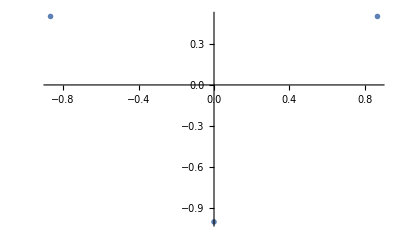

```mathematica
PlotIrrep[defRep]
```

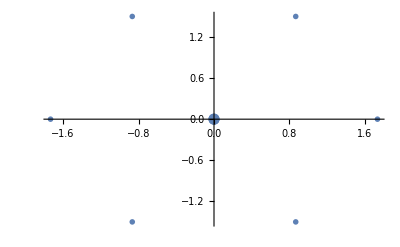

```mathematica
PlotIrrep[adRep]
```

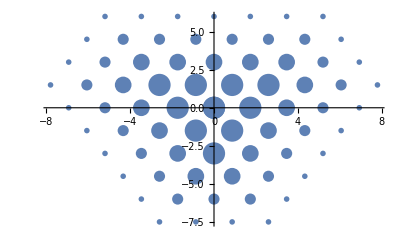

```mathematica
PlotIrrep[Irrep[{6,3}]]
```